```mathematica
Clear[b,k,i,output];
```

```mathematica
Clear[b,k]
```

ArrayPlot::mat: Argument updateLife[{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},«4»,{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}] at position 1 is not a list of lists.

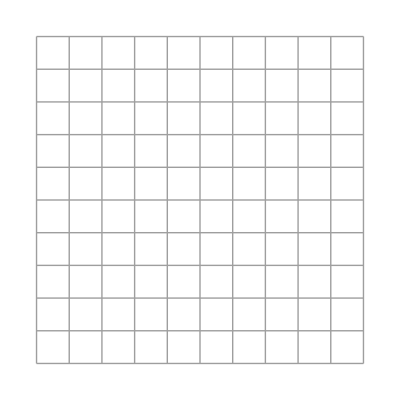
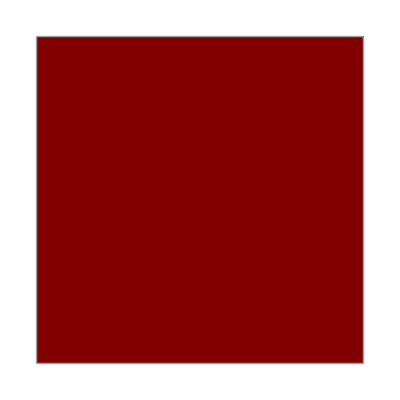
{0.969872,{-Graphics-,{-Graphics-,ArrayPlot[updateLife[{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}],Frame→False,Mesh→True],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
(*Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/life.m"]*)
(*Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf6.m"];*)
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/wordLife.m"];
LIFE=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 1, 1, 0, 1, 1, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
(*LIFE=({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 1, 0}, {0, 1, 1, 1, 1, 0}, {0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 0, 0}});*)

LIFE=ConstantArray[0,{10,10}];
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPAay]*)
AbsoluteTiming[{LIFE//plt,updateIJ[LIFE]//lifePlot}]
```

```mathematica
Get["/home/asdf/Dropbox/05_PROGRAMS/001_LIFE/wordLifeDirectory/wordLife.m"]
```